```mathematica
k11 = 3;
k12 = 1;
k21 = 3;
k31 = 2;
k33 =4;
```

```mathematica
trio=  {
x1'[t] == k11*x1[t]*y1[t] + k12*x1[t]*y2[t], 
x2'[t] == k21*x2[t]*y1[t],
x3'[t] == k31*x3[t]*y1[t] + k33*x3[t]*y3[t],
y1'[t] ==-k11*x1[t]*y1[t] - k21*x2[t]*y1[t] - k31*x3[t]*y1[t],
y2'[t] ==-k12*x1[t]*y2[t] + k21*x2[t]*y1[t],
y3'[t] ==-k33*x3[t]*y3[t] + k12*x1[t]*y2[t],
x1[0] == 1,
x2[0] == 1,
x3[0] == 1,
y1[0] == 1,
y2[0] == 0,
y3[0] == 0};
```

```mathematica
pair12=  {
x1'[t] == k11*x1[t]*y1[t] + k12*x1[t]*y2[t], 
x2'[t] == k21*x2[t]*y1[t],
x3'[t] == k31*x3[t]*y1[t] + k33*x3[t]*y3[t],
y1'[t] ==-k11*x1[t]*y1[t] - k21*x2[t]*y1[t] - k31*x3[t]*y1[t],
y2'[t] ==-k12*x1[t]*y2[t] + k21*x2[t]*y1[t],
y3'[t] ==-k33*x3[t]*y3[t] + k12*x1[t]*y2[t],
x1[0] == 1,
x2[0] == 1,
x3[0] == 0,
y1[0] == 1,
y2[0] == 0,
y3[0] == 0};
```

```mathematica
pair13=  {
x1'[t] == k11*x1[t]*y1[t] + k12*x1[t]*y2[t], 
x2'[t] == k21*x2[t]*y1[t],
x3'[t] == k31*x3[t]*y1[t] + k33*x3[t]*y3[t],
y1'[t] ==-k11*x1[t]*y1[t] - k21*x2[t]*y1[t] - k31*x3[t]*y1[t],
y2'[t] ==-k12*x1[t]*y2[t] + k21*x2[t]*y1[t],
y3'[t] ==-k33*x3[t]*y3[t] + k12*x1[t]*y2[t],
x1[0] == 1,
x2[0] == 0,
x3[0] == 1,
y1[0] == 1,
y2[0] == 0,
y3[0] == 0};
```

```mathematica
pair23=  {
x1'[t] == k11*x1[t]*y1[t] + k12*x1[t]*y2[t], 
x2'[t] == k21*x2[t]*y1[t],
x3'[t] == k31*x3[t]*y1[t] + k33*x3[t]*y3[t],
y1'[t] ==-k11*x1[t]*y1[t] - k21*x2[t]*y1[t] - k31*x3[t]*y1[t],
y2'[t] ==-k12*x1[t]*y2[t] + k21*x2[t]*y1[t],
y3'[t] ==-k33*x3[t]*y3[t] + k12*x1[t]*y2[t],
x1[0] == 0,
x2[0] == 1,
x3[0] == 1,
y1[0] == 1,
y2[0] == 0,
y3[0] == 0};
```

```mathematica
lone=  {
x1'[t] == k11*x1[t]*y1[t] + k12*x1[t]*y2[t], 
x2'[t] == k21*x2[t]*y1[t],
x3'[t] == k31*x3[t]*y1[t] + k33*x3[t]*y3[t],
y1'[t] ==-k11*x1[t]*y1[t] - k21*x2[t]*y1[t] - k31*x3[t]*y1[t],
y2'[t] ==-k12*x1[t]*y2[t] + k21*x2[t]*y1[t],
y3'[t] ==-k33*x3[t]*y3[t] + k12*x1[t]*y2[t],
x1[0] == 0,
x2[0] == 0,
x3[0] == 1,
y1[0] == 1,
y2[0] == 0,
y3[0] == 0};
```

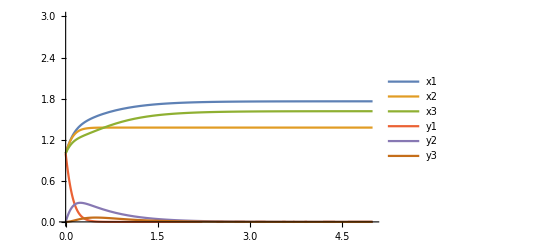

```mathematica
triosol = NDSolve[trio,{x1[t],x2[t],x3[t],y1[t],y2[t],y3[t]},{t,0,10}];
Plot[{x1[t] /.triosol,x2[t]/. triosol,x3[t]/.triosol,y1[t] /.triosol,y2[t] /.triosol,y3[t] /.triosol},{t,0,5},PlotRange-> {0,3},PlotLegends->{"x1","x2","x3","y1","y2","y3"}]
```

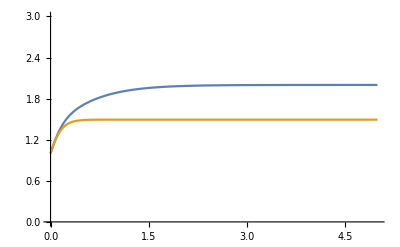

```mathematica
pair12sol = NDSolve[pair12,{x1[t],x2[t],x3[t],y1[t],y2[t],y3[t]},{t,0,10}];
Plot[{x1[t] /.pair12sol,x2[t]/. pair12sol},{t,0,5},PlotRange-> {0,3}]
```

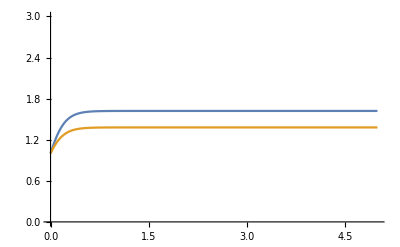

```mathematica
pair13sol = NDSolve[pair13,{x1[t],x2[t],x3[t],y1[t],y2[t],y3[t]},{t,0,10}];
Plot[{x1[t] /.pair13sol,x3[t]/. pair13sol},{t,0,5},PlotRange-> {0,3}]
```

```mathematica
pair23sol = NDSolve[pair23,{x1[t],x2[t],x3[t],y1[t],y2[t],y3[t]},{t,0,10}];
Plot[{x2[t] /.pair23sol,x3[t]/. pair23sol},{t,0,5},PlotRange-> {0,3}]
```

-Graphics-

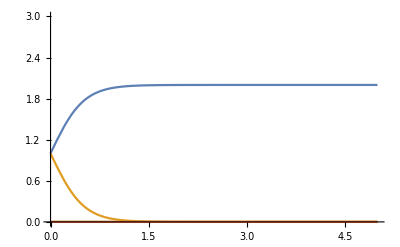

```mathematica
lonesol = NDSolve[lone,{x1[t],x2[t],x3[t],y1[t],y2[t],y3[t]},{t,0,10}];
Plot[{x3[t] /.lonesol,y1[t] /.lonesol,y2[t] /.lonesol,y3[t] /.lonesol},{t,0,5},PlotRange-> {0,3}]
```

```mathematica
relat = (y1[t]/.triosol)/(y1[t]/.pair13sol) + (y1[t]/.triosol)/(y1[t]/.pair23sol) - (y1[t]/.triosol)/(y1[t]/.lonesol) + (k33/k31)*((y3[t]/.triosol)/(y1[t]/.pair13sol) + (y3[t]/.triosol)/(y1[t]/.pair23sol) - (y3[t]/.triosol)/(y1[t]/.lonesol));
```

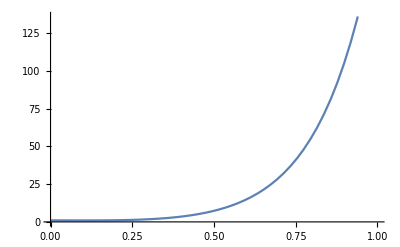

```mathematica
Plot[relat,{t,0,1}]
```